```mathematica
ClearAll["`*"];

(*everything in this cell is just used to make functions*)

(*https://www.myminifactory.com/object/3d-print-batsignal-from-movie-the-dark-knight-rises-2012-73429*)
RECTANGLESSSSS[lx_, hx_, ly_, hy_, lz_, hz_, Color_] := {
ParametricPlot3D[{{a,b,lz}, {a,b,hz} }, {a,lx, hx}, {b, ly, hy}, PlotRange -> All, PlotStyle -> {Color, Color, Color, Color}, Mesh -> None],
ParametricPlot3D[{{a,ly,c}, {a,hy,c} }, {a,lx, hx}, {c, lz, hz}, PlotRange -> All, PlotStyle -> {Color, Color, Color, Color}, Mesh->None],
ParametricPlot3D[{{lx,b,c}, {hx,b,c}},  {b, ly, hy},{c,lz, hz}, PlotRange -> All, PlotStyle -> {Color, Color, Color, Color}, Mesh->None]};

Cloud[ s_, t_, center_, Opacit_] :=ParametricPlot3D[center+  (6.5*(1.5Abs[Sin[s ] Sin[t  1.5]] + 2.5Abs[Cos[t ]Sin[s 0.5]] )+ 5){1.5Sin[s]Sin[t], 2.5Cos[t]Sin[s], Cos[s]}, {s, 0, Pi}, {t, 0, 2Pi}, PlotRange -> All, PlotStyle ->{ Gray, Opacity[Opacit]}, Mesh -> None]

(*BatTubeLine[t_] = {t, t, t};
dirVec1 = {D[BatTubeLine[t], t][[2]], -D[BatTubeLine[t], t][[1]], 0};
dirVec2 = Cross[D[BatTubeLine[t], t], dirVec1];
dirVec1 = dirVec1/Sqrt[dirVec1.dirVec1];
dirVec2 = dirVec2/Sqrt[dirVec2.dirVec2];
^^ ended up not being used for anything but I'm leaving it bc why not
*)
BetterTube[s_, t_, r_,dirVec1_, center_, Color_ , sstart_, send_, Opacit_] := ParametricPlot3D[center + dirVec1*s +  r (Cos[t] * {dirVec1[[2]], -dirVec1[[1]], 0}/Sqrt[dirVec1[[1]]^2 + dirVec1[[2]]^2] + Sin[t] * (Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ]/(Sqrt[Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ].Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ]]))), {s, sstart, send}, {t, 0 ,2Pi}, PlotRange -> All, PlotStyle -> {Color, Opacity[Opacit]}, Mesh -> None]

BetterTubeCaps[rad_, t_, r_,dirVec1_, center_, Color_ , sstart_, send_, Opacit_]  := ParametricPlot3D[{center + dirVec1*sstart +  r (Cos[t] * {dirVec1[[2]], -dirVec1[[1]], 0}/Sqrt[dirVec1[[1]]^2 + dirVec1[[2]]^2] + Sin[t] * (Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ]/(Sqrt[Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ].Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ]]))), center + dirVec1*send +  r (Cos[t] * {dirVec1[[2]], -dirVec1[[1]], 0}/Sqrt[dirVec1[[1]]^2 + dirVec1[[2]]^2] + Sin[t] * (Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ]/(Sqrt[Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ].Cross[dirVec1,{dirVec1[[2]], -dirVec1[[1]], 0} ]])))}, {r, 0, rad}, {t, 0 ,2Pi}, PlotRange -> All, PlotStyle -> {{Color,Opacity[Opacit]}, {Color, Opacity[Opacit]}}, Mesh -> None]

AngledColumn[ start_, t_,a_, tlow_, thigh_, alow_, ahigh_,dirVec1_,dirVec2_, change_,  Color_] := {
ParametricPlot3D[start + dirVec2 * a+ dirVec1*t, {a,alow, ahigh}, {t, tlow, thigh}, PlotRange -> All, PlotStyle -> {Color}], 
ParametricPlot3D[start + change + dirVec2 * a+ dirVec1*t ,  {a,alow, ahigh}, {t, tlow, thigh}, PlotRange -> All, PlotStyle -> {Color}],
ParametricPlot3D[start + dirVec1 * t + change * b + dirVec2 * alow, {b,0,1}, {t, tlow, thigh}, PlotRange -> All, PlotStyle -> {Color}], 
ParametricPlot3D[start +  dirVec1 * t + change * b + dirVec2 * ahigh, {b,0,1}, {t, tlow, thigh}, PlotRange -> All, PlotStyle -> {Color}],ParametricPlot3D[start + dirVec2 * a + change * b + dirVec1 * tlow, {b,0,1},  {a,alow, ahigh}, PlotRange -> All, PlotStyle -> {Color}], 
ParametricPlot3D[start +  dirVec2 * a + change * b + dirVec1 * thigh, {b,0,1},  {a,alow, ahigh}, PlotRange -> All, PlotStyle -> {Color}]};

BatTrianglesofPOWER[r_, h_,s_,t_,Color_, stheta_, etheta_, anglecoord_, change_ ,changedirvec_] :={ ParametricPlot3D[{anglecoord + r h Sec[s]{Cos[t] Sin[s], Sin[t] Sin[s], Cos[s]},change + anglecoord + r h Sec[s]{Cos[t] Sin[s], Sin[t] Sin[s], Cos[s]}} , {r, 0, 1}, {s, stheta, etheta}, PlotStyle->{Color, Color}], ParametricPlot3D[anglecoord + changedirvec*change u + {1, Sin[t], 1}*{0,Sin[stheta], Cos[stheta]}*v, {u, 0, 1}, {v, 0, h Sec[stheta]}, PlotStyle -> Color]}


FourierCurve[x_, m_, t_, tol_: 0.0000001] := Module[{rat = Rationalize[#, tol] &, fc},
  fc = Take[Chop[Fourier[x, FourierParameters -> {-1, 1}]], Min[m, Ceiling[Length[x]/2]]];
  2 rat[Abs[fc]].Cos[Pi (2 Range[0, Length[fc] - 1] t - rat[Arg[fc]/Pi])]]
 tocurve[Line[data_], m_, t_] := FourierCurve[#, m, t] & /@ Transpose[data]
dat = ImageValuePositions[
   SelectComponents[EdgeDetect@ColorNegate@Binarize@-Graphics-,
    Large], 1];
batLogo[t_] = tocurve[#, 100, t] & /@ {Line[dat[[Last[FindShortestTour[dat]]]]]};
```

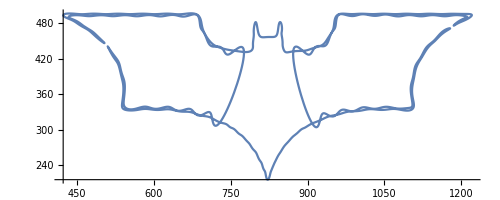

```mathematica
ParametricPlot[batLogo[t], {t, 0, 1}]
```

```mathematica
(*this is the base, also if you are reading this, i tossed in random lines that do nothing for the fun of it, good luck finding them :) *)
gothampdtower = RECTANGLESSSSS[-8, 8, -7, 7, 0,25, Darker[GrayLevel[0],5/6]];
pedestal = RECTANGLESSSSS[-5, 5, -5, 5, 25,26, Black];

pedestalcirc =ParametricPlot3D[{0,0,25.9} + {0,0,0.6}*s +  4.5(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0}), {s, 0, 1}, {t, 0 ,2Pi}, PlotRange -> All, PlotStyle -> Black];
pedestaltop = ParametricPlot3D[{0,0,26.5}+s{Cos[t], Sin[t], 0}, {s, 0, 4.5}, {t, 0 ,2Pi}, PlotRange -> All, PlotStyle -> Black];
set1 = {gothampdtower, pedestal,pedestalcirc, pedestaltop};
set2 = {pedestal,pedestalcirc, pedestaltop};
```

```mathematica
(*these are the screws (i know i know, they are definitely important enough to get their own lines of code) *)
screwsbottom = ParametricPlot3D[{{4.5,4.7,26}+r{Cos[t], Sin[t], 0}, {4.7,4.5,26}+r{Cos[t], Sin[t], 0}, {-4.5,4.7,26}+r{Cos[t], Sin[t], 0}, {-4.7,4.5,26}+r{Cos[t], Sin[t], 0},{4.5,-4.7,26}+r{Cos[t], Sin[t], 0}, {4.7,-4.5,26}+r{Cos[t], Sin[t], 0},{-4.5,-4.7,26}+r{Cos[t], Sin[t], 0}, {-4.7,-4.5,26}+r{Cos[t], Sin[t], 0}}, {r, 0, 0.1}, {t, 0 ,2Pi}, PlotRange -> All, PlotStyle -> {Black,Black,Black,Black,Black,Black,Black,Black}];
screwstop = ParametricPlot3D[{{4.5,4.7,26} + {0,0,0.25}*s +  0.075(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0}), {4.7,4.5,26} + {0,0,0.25}*s +  0.075(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0}), {-4.5,4.7,26} + {0,0,0.25}*s +  0.075(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0}), {-4.7,4.5,26} + {0,0,0.25}*s +  0.075(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0}), {4.5,-4.7,26} + {0,0,0.25}*s +  0.075(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0}), {4.7,-4.5,26} + {0,0,0.25}*s +  0.075(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0}), {-4.5,-4.7,26} + {0,0,0.25}*s +  0.075(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0}), {-4.7,-4.5,26} + {0,0,0.25}*s +  0.075(Cos[t] * {1,0, 0}+ Sin[t] {0,1,0})}, {s, 0, 1}, {t, 0 ,2Pi}, PlotRange -> All, PlotStyle -> {Black,Black,Black,Black,Black,Black,Black,Black}];
screws = {screwsbottom, screwstop};
```

```mathematica
(*this makes the u-shaped thingy*)
```

```mathematica
merrychristmas = m E^(rry) x-mas!;
le = 3.5
bottomthingamablob =  RECTANGLESSSSS[-le, le, -0.8, 0.8, 26.5,28, Black];
a = le*2/7;
smallthingyp1 = {RECTANGLESSSSS[-le+a, -le+2a, -1.6, -0.8, 26.5,27.2, Black],RECTANGLESSSSS[-le+3a, -le+4a, -1.6, -0.8, 26.5,27.2, Black],RECTANGLESSSSS[-le+5a, -le+6a, -1.6, -0.8, 26.5,27.2, Black],RECTANGLESSSSS[-le+a, -le+2a, 0.8,1.6, 26.5,27.2, Black],RECTANGLESSSSS[-le+3a, -le+4a, 0.8,1.6, 26.5,27.2, Black],RECTANGLESSSSS[-le+5a, -le+6a, 0.8,1.6, 26.5,27.2, Black]};
smallthingyp2 = { BatTrianglesofPOWER[r,-0.8, s, Pi/2, Black, 3Pi/4, Pi, {-le+a,0.8,28}, {a, 0, 0}, {1,0,0}] , BatTrianglesofPOWER[r,-0.8, s, Pi/2, Black, 3Pi/4, Pi, {-le+3a,0.8,28}, {a, 0, 0}, {1,0,0}] , BatTrianglesofPOWER[r,-0.8, s, Pi/2, Black, 3Pi/4, Pi, {-le+5a,0.8,28}, {a, 0, 0}, {1,0,0}] , BatTrianglesofPOWER[r,-0.8, s, 3Pi/2, Black, 3Pi/4, Pi, {-le+a,-0.8,28}, {a, 0, 0}, {1,0,0}] , BatTrianglesofPOWER[r,-0.8, s, 3Pi/2, Black, 3Pi/4, Pi, {-le+3a,-0.8,28}, {a, 0, 0}, {1,0,0}] , BatTrianglesofPOWER[r,-0.8, s, 3Pi/2, Black, 3Pi/4, Pi, {-le+5a,-0.8,28}, {a, 0, 0}, {1,0,0}] };
sidethingy = {BatTrianglesofPOWER[r, 1.5,s,0,Black, 3 Pi/4, Pi,{-le,-0.8,26.5}, {0, 1.6, 0} ,{0,1,0}], BatTrianglesofPOWER[r, 1.5,s,Pi,Black, 3 Pi/4, Pi,{le,-0.8,26.5}, {0, 1.6, 0} ,{0,1,0}]};
fixer = {smallthingyp1, smallthingyp2, sidethingy, ParametricPlot3D[{{-1, 0, 1}help + {0, 1, 0}me + {-le,-0.8,26.5}, {1, 0, 1}help + {0, 1, 0}me + {le,-0.8,26.5}}, {help, 0, 1.5}, {me, 0, 1.6}, PlotStyle -> {Black, Black}], ParametricPlot3D[{{0,1,0}help + {-1,0,0}me + {-le,-0.8,28}, {0,1,0}help + {1,0,0}me + {le,-0.8,28}},{help, 0, 1.6}, {me, 0, 1.5}, PlotStyle -> {Black, Black}]};
lng = 5;
heights = {RECTANGLESSSSS[-le-1.5, -le-1, -0.8, 0.8, 28, 28+lng, Black], RECTANGLESSSSS[le+1.5, le+1, -0.8, 0.8, 28, 28+lng, Black]};
set3 = {bottomthingamablob, smallthingyp1, smallthingyp2, sidethingy, fixer, heights};
```

3.5

```mathematica
(*and it is at thi s point that I gave up on commenting the code, if you are actually reading these you are a real one*)
dirvec = {0,1,1};
dirvec2 = {0,-1,1};
dirvec2 = dirvec2/Sqrt[dirvec2.dirvec2];
dirvec3 = Cross[dirvec, dirvec2];
dirvec3 = dirvec3/Sqrt[dirvec3.dirvec3];
le = 3.5;
lng = 5;
lefor = 5;
lebac = -2;
le3 = 1;
alph = 0.5;
morescrews = {BetterTube[s,t,0.4, dirvec3, {le+1, 0, 28+lng-alph}, Black, 0, 0.6, 1], BetterTube[s,t,0.4, dirvec3, {-le-1, 0, 28+lng-alph}, Black, -0.6, 0, 1], BetterTubeCaps[0.4,t,r, dirvec3, {le+1, 0, 28+lng-alph},Black, 0, 0.6, 1], BetterTubeCaps[0.4,t,r, dirvec3, {-le-1, 0, 28+lng-alph},Black, -0.6, 0, 1]};
glass = {BetterTube[s,t,le+1, dirvec, {0,0,28+lng},LightBlue,lebac, lefor, 0.3], BetterTubeCaps[le+1,t,r, dirvec, {0,0,28+lng},LightBlue, lebac, lefor, 0.3]};
edges1 = {AngledColumn[ {-le-1, 0, 28+lng}-dirvec2*0.25, t,g, lebac+0.2, lefor, -0.5,0.5,dirvec,dirvec2, dirvec3*-0.4,  Black],AngledColumn[ {le+1, 0, 28+lng}-dirvec2*0.25, t,g, lebac+0.2, lefor, -0.5,0.5,dirvec,dirvec2, dirvec3*0.4,  Black],
AngledColumn[ {0, 0, 28+lng } + (le+1)dirvec2 , t,g, lebac+0.2, lefor, -0.5,0.5,dirvec,dirvec3, dirvec2*0.4,  Black],
AngledColumn[ {0, 0, 28+lng }- (le+1)dirvec2 , t,g, lebac+0.2, lefor, -0.5,0.4,dirvec,dirvec3, dirvec2*-0.4,  Black]};
edges2 = {BetterTube[s,t, le+1.2, dirvec, {0, 0,28+lng}+dirvec*(lebac-0.25), Black,  0, le3, 1],BetterTube[s,t, le+1.05, dirvec, {0, 0,28+lng}+dirvec*(lebac+0.25), Black,  0, le3+1, 1]};
edge3 = ParametricPlot3D[{0, 0,28+lng}+dirvec*(lebac-0.25) +  r (Cos[t] * dirvec2 + Sin[t] * (dirvec3)),{r, 0, le+1.21}, {t, 0 ,2Pi}, PlotRange -> All, PlotStyle -> Black, Mesh -> None];
lj = (lefor-lebac)/5;
rings = {BetterTube[s,t,le+1.05, dirvec, {0, 0,28+lng}+dirvec * (lj+lebac-0.25), Black, 0, lj/3, 1],
BetterTube[s,t,le+1.05, dirvec, {0, 0,28+lng}+dirvec * (2lj+lebac-0.25), Black, 0, lj/3, 1],
BetterTube[s,t,le+1.05, dirvec, {0, 0,28+lng}+dirvec * (3lj+lebac-0.25), Black, 0, lj/3, 1],
BetterTube[s,t,le+1.05, dirvec, {0, 0,28+lng}+dirvec * (4lj+lebac-0.25), Black, 0, lj/3, 1],
BetterTube[s,t,le+1.05, dirvec, {0, 0,28+lng}+dirvec * (5lj+lebac-0.25), Black, 0, lj/3, 1],
ParametricPlot3D[{0, 0,28+lng}+dirvec*((5+1/3)lj+lebac-0.25) +  r (Cos[t] * dirvec2 + Sin[t] * (dirvec3)),{r, le+0.8, le+1.21}, {t, 0 ,2Pi}, PlotRange -> All, PlotStyle -> Black, Mesh -> None]};
set4 = {glass, edges1, edges2, edge3, rings};
Show[set2, screws,set3,set4,morescrews, Axes -> True]
```

-Graphics3D-

```mathematica
nbatLogo[t_] = {batLogo[t][[1]][[1]], 0,  batLogo[t][[1]][[2]]};
scale = 0.009;
tab2 = scale *  Table[nbatLogo[t], {t,0.55, 0.74, 0.001}];
tab3 =  scale * Table[nbatLogo[t], {t, 0.25, 1, 0.001}];

tab2 = tab2//.{x_List}:>x;
tab3 = tab3//.{x_List}:>x;
bsf1=BSplineFunction[tab2,SplineClosed->True];
dat1=Table[bsf1[t],{t,0,1,.01}];
th1 = Graphics3D[{Black,EdgeForm[Directive[LightGray,Thin]],Translate[Rotate[Polygon[dat1], 45Degree, {1,0,0}],  {0, 0, 28+lng } + (le-1)dirvec2+ {-7.5,7.5, 0}+ dirvec*1.5]}];

bsf2=BSplineFunction[tab3,SplineClosed->True];
dat2=Table[bsf2[t],{t,0,1,.01}];
th2 = Graphics3D[{Black,EdgeForm[Directive[LightGray,Thin]],Translate[Rotate[Polygon[dat2], 45Degree, {1,0,0}],  {0, 0, 28+lng } + (le-1)dirvec2+ {-7.5,7.5, 0} + dirvec*1.5] }];
thelegendbegins = {th1, th2};
Show[set2, screws,set3,set4,thelegendbegins, Axes -> True]
Show[set1, screws,set3,set4,thelegendbegins, Axes -> True]
Show[set1, screws,set3,set4,thelegendbegins, Axes -> True]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
siz= 60;
light = ParametricPlot3D[{0, 0,28+lng}+dirvec*lefor+(le+1+0.2s)*(Cos[t]dirvec2 + Sin[t]dirvec3 )+ dirvec*s, {s, 0, siz}, {t, 0, 2Pi}, PlotStyle -> {Lighter[Yellow], Opacity[0.3]}, Mesh -> None];
cloud = Cloud[s,t,{0, 0,28+lng}+dirvec*(lefor+siz+8), 0.3];
sca = (le+1+0.2 siz)/(le+1);
cloudlight = ParametricPlot3D[{0, 0,28+lng}+dirvec*(lefor+siz) + r(dirvec2 Cos[t] + dirvec3 Sin[t]), {t, 0, 2Pi}, {r, 0, (le+1+0.2*siz)}, PlotStyle -> {Lighter[Yellow], Opacity[0.4]}, Mesh -> None];
thelegendcontinues = Graphics3D[{Black,EdgeForm[Directive[Black,Thin]],Translate[Rotate[Scale[{Polygon[dat1], Polygon[dat2]}, sca], 45Degree, {1,0,0}],  {0, 0, 28+lng } + (le-1)dirvec2+ {-7.5,7.5, 0}+ dirvec*1.5+dirvec*siz]}];
Show[set1, screws,set3,set4,thelegendbegins,light,thelegendcontinues, cloudlight, cloud,  Axes -> True, PlotRange -> All]
```

-Graphics3D-